```mathematica
(*parmeters*)
kEcat=1;
KEacetate=0.1;
KFbpFBP=0.1;
vFbpmax=1;
Lfbp=4*^6;
KFbpPEP=0.1;
vEXmax=1;
KEXPEP=0.3;
vemax=1.1;
KeFBP=0.45;
ne=2;
acetate=0.1;
d=0.25;
kPEPout=0;

flux1[z_]:=kEcat*z*acetate/(acetate+KEacetate);
flux2[y_] :=vemax*(1-1/(1+(KeFBP/y)^ne));
flux3[x_,y_]:=vFbpmax*(y/KFbpFBP)*(1+y/KFbpFBP)^3/((1+y/KFbpFBP)^4+Lfbp*(1+x/KFbpPEP)^(-4));
flux4[x_]:=vEXmax*x/(x+KEXPEP);
flux5[x_]:=kPEPout*x;

f1[x_,y_,z_]:=flux1[z]-flux4[x]-flux5[x];
f2[x_,y_,z_]:=flux4[x]-flux3[x,y];
f3[x_,y_,z_]:=flux2[y]-d*z;

(*contour plots of nullclines*)
flux1p=kEcat*z*acetate/(acetate+KEacetate);
flux2p =vemax*(1-1/(1+(KeFBP/y)^ne));
flux3p=vFbpmax*(y/KFbpFBP)*(1+y/KFbpFBP)^3/((1+y/KFbpFBP)^4+Lfbp*(1+x/KFbpPEP)^(-4));
flux4p=vEXmax*x/(x+KEXPEP);
flux5p=kPEPout*x;
f1p=flux1p-flux4p-flux5p;
f2p=flux4p-flux3p;
f3p=flux2p-d*z;

cc1 = ContourPlot3D[{f1[x,y,z]==0,f2[x,y,z]==0},{x,0.01,5},{y,0.01,5},{z,0.01,5},MeshFunctions->{Function[{x,y,z,f},f1p-f2p]},MeshStyle->{{Dashed,Blue}},ContourStyle->None,Mesh->{{0}},BoundaryStyle->None,Axes->True,AxesLabel->{PEP,FDP,Enzyme},AxesStyle->Directive[Black, 12]];
cc1points = Cases[Normal@cc1,Line[x_]:>x,Infinity];
cc2 = ContourPlot3D[{f1[x,y,z]==0,f3[x,y,z]==0},{x,0.01,5},{y,0.01,5},{z,0.01,5},MeshFunctions->{Function[{x,y,z,f},f1p-f3p]},MeshStyle->{{Dashed,Magenta}},ContourStyle->None,Mesh->{{0}},BoundaryStyle->None,Axes->True,AxesLabel->{PEP,FDP,Enzyme},AxesStyle->Directive[Black, 12]];
cc2points = Cases[Normal@cc2,Line[x_]:>x,Infinity];
cc3 = ContourPlot3D[{f2[x,y,z]==0,f3[x,y,z]==0},{x,0.01,5},{y,0.01,5},{z,0.01,5},MeshFunctions->{Function[{x,y,z,f},f2p-f3p]},MeshStyle->{{Dashed,Cyan}},ContourStyle->None,Mesh->{{0}},BoundaryStyle->None,Axes->True,AxesLabel->{PEP,FDP,Enzyme},AxesStyle->Directive[Black, 12]];
cc3points = Cases[Normal@cc3,Line[x_]:>x,Infinity];
Show[cc1,cc2,cc3]
(*Show[cc1,cc2,cc3,ViewPoint->{Infinity,0,0}]
Show[cc1,cc2,cc3,ViewPoint->{0,-Infinity,0}]
Show[cc1,cc2,cc3,ViewPoint->{0,0,-Infinity}]*)

(*all together contour plot*)
(*ContourPlot3D[{f1[x,y,z]==0,f2[x,y,z]==0,f3[x,y,z]==0},{x,0.01,5},{y,0.01,5},{z,0.01,5},MeshFunctions->{Function[{x,y,z,f},f1p-f2p],Function[{x,y,z,f},f1p-f3p],Function[{x,y,z,f},f2p-f3p]},MeshStyle->{{Thick,Blue},{Thick,Magenta},{Thick,Cyan}},ContourStyle->None,Mesh->{{0}},BoundaryStyle->None,Axes->True,AxesLabel->{PEP,FDP,Enzyme},AxesStyle->Directive[Black, 12]]*)

(*solve numerical system*)
eqsols = NSolve[{f1[x,y,z]==0,f2[x,y,z]==0,f3[x,y,z]==0},{x,y,z},Reals];
(*get only poistive solutions*)
eqsols = {x,y,z}/.Select[eqsols,!MemberQ[Values[#],x_/;x<0]&];
pp =ListPointPlot3D[eqsols,PlotStyle-> Directive[Red,PointSize[Large]]];
Show[pp,cc1,cc2,cc3]

(*vector plots*)
v = VectorPlot3D[{f1[x,y,z],f2[x,y,z],f1[x,y,z]-f2[x,y,z]},{x,0.01,5},{y,0.01,5},{z,0.01,5},VectorPoints->50,VectorColorFunction->"Rainbow"]

Show[{v,cc1,pp},Axes-> True,AxesLabel-> {PEP,FDP,Enzyme}]

(*RegionPlot3D[f1[x,y,z]<=1*^-12&&f2[x,y,z]<=1*^-12&&f3[x,y,z]<=1*^-12,{x,0.001,5},{y,0.001,5},{z,0.001,5}]*)
(*Show[cc1,pp,v]*)
(*Show[{cc1,cc2,cc3,pp},Axes-> True,AxesLabel-> {PEP,FDP,Enzyme}]*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Show[%3260,ViewPoint->{0,0,∞}]
```

```mathematica
Show[%3285,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\shyam\\Desktop\\pepvfdp.jpg",%3286,"JPEG"]
```

C:\Users\shyam\Desktop\pepvfdp.jpg

```mathematica
Show[%3260,ViewPoint->{0,-∞,0}]
```

```mathematica
Show[%3279,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\shyam\\Desktop\\pepvenzyme.jpg",%3280,"JPEG"]
```

C:\Users\shyam\Desktop\pepvenzyme.jpg

```mathematica
Show[%3260,ViewPoint->{∞,0,0}]
```

```mathematica
Show[%3272,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\shyam\\Desktop\\fdpvenzyme.jpg",%3273,"JPEG"]
```

C:\Users\shyam\Desktop\fdpvenzyme.jpg

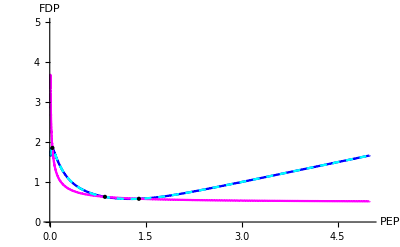

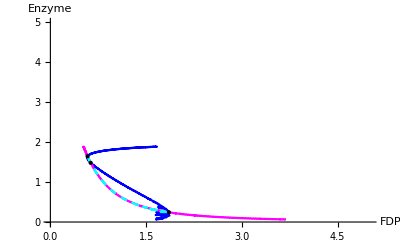

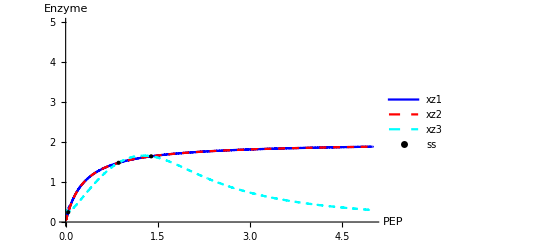

```mathematica
(*Nullclines and points of intersection in 2D with SS(points of interescetion of all nullclines) shown with dots*)
cc1fp =Flatten[cc1points,1];
cc2fp =Flatten[cc2points,1];
cc3fp =Flatten[cc3points,1];

xycc1points=Table[cc1fp[[i,{1,2}]],{i,1,Dimensions[cc1fp][[1]]}];
xycc1points=Sort[xycc1points,#1[[1]]<#2[[1]]&];
xycc2points=Table[cc2fp[[i,{1,2}]],{i,1,Dimensions[cc2fp][[1]]}];
xycc2points=Sort[xycc2points,#1[[1]]<#2[[1]]&];
xycc3points=Table[cc3fp[[i,{1,2}]],{i,1,Dimensions[cc3fp][[1]]}];
xycc3points=Sort[xycc3points,#1[[1]]<#2[[1]]&];

xy1=ListPlot[xycc1points,DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Blue},Joined->True];
xy2=ListPlot[xycc2points,DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Magenta},Joined->True];
xy3=ListPlot[xycc3points,DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Cyan,Dashed},Joined->True];
ssxy = ListPlot[Table[eqsols[[i,{1,2}]],{i,1,Dimensions[eqsols][[1]]}],PlotStyle->Directive[Black,PointSize[Large]]];
Show[{xy1,xy2,xy3,ssxy},AspectRatio->1/GoldenRatio,Axes->True,AxesLabel->{PEP,FDP},AxesOrigin->{0,0},PlotRange->{0,5}]

yzcc1points=Table[cc1fp[[i,{2,3}]],{i,1,Dimensions[cc1fp][[1]]}];
yzcc1points=Sort[yzcc1points,#1[[2]]<#2[[2]]&];
yzcc2points=Table[cc2fp[[i,{2,3}]],{i,1,Dimensions[cc2fp][[1]]}];
yzcc2points=Sort[yzcc2points,#1[[2]]<#2[[2]]&];
yzcc3points=Table[cc3fp[[i,{2,3}]],{i,1,Dimensions[cc3fp][[1]]}];
yzcc3points=Sort[yzcc3points,#1[[2]]<#2[[2]]&];

yz1=ListPlot[{yzcc1points},DataRange->{0.01,5},MaxPlotPoints->All,Joined->True,PlotStyle->{Blue},InterpolationOrder-> 3];
yz2=ListPlot[{yzcc2points},DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Magenta},Joined->True];
yz3=ListPlot[{yzcc3points},DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Cyan,Dashed},Joined->True];
ssyz = ListPlot[Table[eqsols[[i,{2,3}]],{i,1,Dimensions[eqsols][[1]]}],PlotStyle->Directive[Black,PointSize[Large]]];
Show[{yz1,yz2,yz3,ssyz},AspectRatio->1/GoldenRatio,Axes->True,AxesLabel->{FDP,Enzyme},AxesOrigin->{0,0},PlotRange->{{0,5},{0,5}}]

xzcc1points=Table[cc1fp[[i,{1,3}]],{i,1,Dimensions[cc1fp][[1]]}];
xzcc1points=Sort[xzcc1points,#1[[1]]<#2[[1]]&];
xzcc2points=Table[cc2fp[[i,{1,3}]],{i,1,Dimensions[cc2fp][[1]]}];
xzcc2points=Sort[xzcc2points,#1[[1]]<#2[[1]]&];
xzcc3points=Table[cc3fp[[i,{1,3}]],{i,1,Dimensions[cc3fp][[1]]}];
xzcc3points=Sort[xzcc3points,#1[[1]]<#2[[1]]&];

xz1=ListPlot[{xzcc1points},DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Blue},Joined->True,InterpolationOrder-> 3,PlotLegends->{"xz1"}];
xz2=ListPlot[{xzcc2points},DataRange->{0.01,5},MaxPlotPoints->All,PlotStyle->{Red,Dashed},Joined->True,PlotLegends->{"xz2"}];
xz3=ListPlot[{xzcc3points},DataRange->{0.01,5},MaxPlotPoints->All,InterpolationOrder->3,PlotStyle->{Cyan,Dashed},Joined->True,PlotLegends->{"xz3"}];
ssxz = ListPlot[Table[eqsols[[i,{1,3}]],{i,1,Dimensions[eqsols][[1]]}],PlotStyle->Directive[Black,PointSize[Large]],PlotLegends->{"ss"}];
Show[{xz1,xz2,xz3,ssxz},AspectRatio->1/GoldenRatio,Axes->True,AxesLabel->{PEP,Enzyme},AxesOrigin->{0,0},PlotRange->{{0,5},{0,5}}]

(*Table[eqsols[[i,{2,3}]],{i,1,Dimensions[eqsols][[1]]}]
Table[eqsols[[i,{1,3}]],{i,1,Dimensions[eqsols][[1]]}]
SetDirectory[NotebookDirectory[]];
Export["xzcc3.xls",xzcc3points]*)
```

{{0.0417371,1.85612,0.244264},{0.862298,0.630867,1.48378},{1.39358,0.582154,1.64572}}

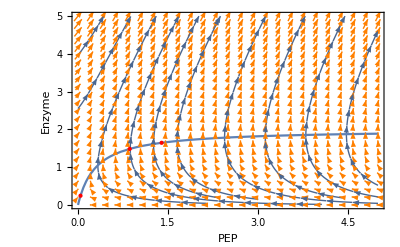

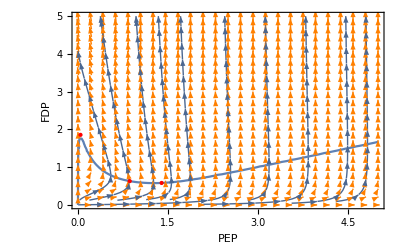

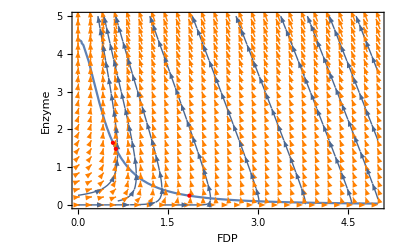

```mathematica
(*solve numerical system*)
eqsols = NSolve[f1[x,y,z]==0&&f2[x,y,z]==0&&f3[x,y,z]==0,{x,y,z},Reals];
(*get only poistive solutions*)
eqsols = {x,y,z}/.Select[eqsols,!MemberQ[Values[#],x_/;x<0]&]
f12d[x_,z_]:=flux1[z]-flux4[x]-flux5[x];
f22d[x_,y_]:=flux4[x]-flux3[x,y];
f32d[y_,z_]:=flux2[y]-d*z;

upl = 5;
vp1 = VectorPlot[{f12d[x,z],z},{x,0,upl},{z,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp1 = ListPlot[Table[eqsols[[i,{1,3}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp1=ContourPlot[f12d[x,z]==0,{x,0,upl},{z,0,upl}];
Show[{vp1,cp1,lp1},Axes-> True,AxesLabel-> {PEP,Enzyme},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]

vp2 = VectorPlot[{f22d[x,y],y},{x,0,upl},{y,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp2 = ListPlot[Table[eqsols[[i,{1,2}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp2=ContourPlot[f22d[x,y]==0,{x,0,upl},{y,0,upl}];
Show[{vp2,cp2,lp2},Axes-> True,AxesLabel-> {PEP,FDP},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]

vp3 = VectorPlot[{f32d[y,z],z},{y,0,upl},{z,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp3 = ListPlot[Table[eqsols[[i,{2,3}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp3=ContourPlot[f32d[y,z]==0,{y,0,upl},{z,0,upl}];
Show[{vp3,cp3,lp3},Axes-> True,AxesLabel-> {FDP,Enzyme},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]
```

```mathematica
(*tt = Table[Positive[Values[sol[[i]]]],{i,1,6}]
Select[Positive[Values[sol]],!MemberQ[#,False]&]*)

(*MemberQ[Table[Positive[{x,y,z}/.sol[[i]]],{i,1,1}],TrueQ,2]*)
```

{{0.244262,0.0417335,1.85613},{1.48446,0.863055,0.630648},{1.64602,1.39234,0.582071}}